```mathematica
SetDirectory["/Users/davidnordfors/galvanize/galvanize-capstone"]
```

/Users/davidnordfors/galvanize/galvanize-capstone

```mathematica
abilities = Import["/Users/davidnordfors/galvanize/galvanize-capstone/data/DoL/db_23_2_excel/Abilities.xlsx"];
```

```mathematica
abilities = abilities[[1]]
```

{{O*NET-SOC Code,Title,Element ID,Element Name,Scale ID,Scale Name,Data Value,N,Standard Error,Lower CI Bound,Upper CI Bound,Recommend Suppress,Not Relevant,Date,Domain Source},100567,{53-7121.00,Tank Car, Truck, and Ship Loaders,1.A.4.b.5,Speech Clarity,LV,Level,2.88,8.,0.13,2.63,3.12,N,N,12/2006,Analyst}}
 |  |  |  |

```mathematica
dab = AssociationThread[abilities[[1]] -> Transpose[abilities[[2;;]]]];
```

```mathematica
indexit[names_List]:= AssociationThread[# -> Range[Length[#]]]&@ DeleteDuplicates[names];
```

```mathematica
abilityindex= indexit[dab["Element ID"]];
soccodeindex = indexit[dab["O*NET-SOC Code"]];
```

```mathematica
soc2title=DeleteDuplicates[Thread[dab["O*NET-SOC Code"]->dab["Title"]]];
elementid2ability =AssociationThread[dab["Element ID"]->dab["Element Name"]];
```

```mathematica
ab1 = abilities[[#]]&/@Range[3,Length[abilities],2]
```

{{11-1011.00,Chief Executives,1.A.1.a.1,Oral Comprehension,LV,Level,4.88,8.,0.13,4.63,5.12,N,N,07/2014,Analyst},50282,{53-7121.00,Tank Car, Truck, and Ship Loaders,1.A.4.b.5,Speech Clarity,LV,Level,2.88,8.,0.13,2.63,3.12,N,N,12/2006,Analyst}}
 |  |  |  |

```mathematica
edges = {#[[1]], #[[3]]}->#[[7]]&/@ab1[[;;-1]];
```

```mathematica
edges[[;;10]]
```

{{11-1011.00,1.A.1.a.1}→4.88,{11-1011.00,1.A.1.a.2}→4.62,{11-1011.00,1.A.1.a.3}→5.,{11-1011.00,1.A.1.a.4}→4.62,{11-1011.00,1.A.1.b.1}→4.62,{11-1011.00,1.A.1.b.2}→4.25,{11-1011.00,1.A.1.b.3}→5.,{11-1011.00,1.A.1.b.4}→5.,{11-1011.00,1.A.1.b.5}→5.,{11-1011.00,1.A.1.b.6}→4.}

```mathematica
sparse = SparseArray[edges/. abilityindex /. soccodeindex];
```

```mathematica
sparse
```

SparseArray[<43363>, {967, 52}]

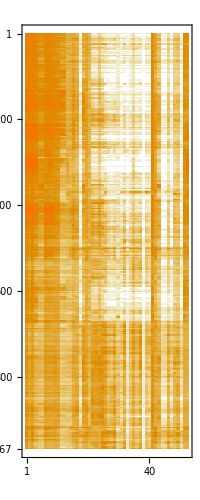

```mathematica
MatrixPlot[%573]
```

```mathematica
{u,w,v}=SingularValueDecomposition[N[sparse],12];
```

```mathematica
Diagonal[Normal[w]]
```

```mathematica
{548.975105114762,147.18399957574263,45.80824490426022,43.94226016452456,28.101383382568137,23.69401120992566,22.615751534275205,19.128830198990844,18.247659013568995,17.011245376769544,16.214715826105547,14.894835330340939,13.810973464319476,13.052754144315816,12.927579178269458,12.147817778157082,11.903605483764702,10.789220549656443,10.473602085339992,10.103756487006747}
```

{548.975,147.184,45.8082,43.9423,28.1014,23.694,22.6158,19.1288,18.2477,17.0112,16.2147,14.8948,13.811,13.0528,12.9276,12.1478,11.9036,10.7892,10.4736,10.1038}

```mathematica
wtot = Total[%579]
```

1256.46

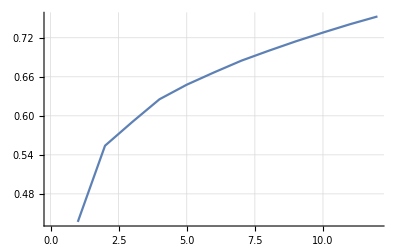

```mathematica
ListLinePlot[Accumulate[Diagonal[Normal[w]]]/wtot,GridLines->Automatic]
```

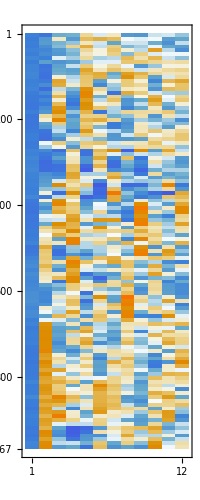
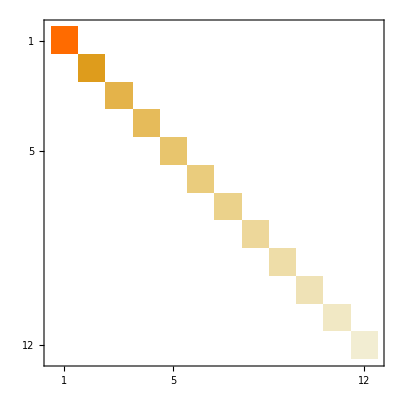
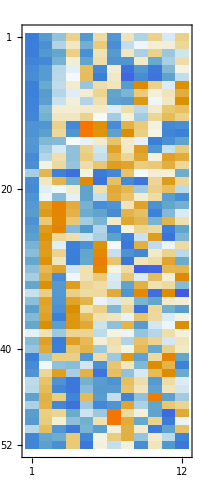

```mathematica
{MatrixPlot[u],MatrixPlot[w],MatrixPlot[v]}
```

```mathematica
abilitytopics = Round[Select[ReverseSort[AssociationThread[Keys[abilityindex]->#^2]],#>0.001&],0.0001]&/@Transpose[v];
abilitops = (Normal[abilitytopics ]/. elementid2ability)/.Rule :> List;
MatrixForm/@Normal[abilitops]
```

{(Oral Comprehension | 0.0504
Oral Expression | 0.0486
Written Comprehension | 0.0435
Near Vision | 0.0423
Problem Sensitivity | 0.0415
Deductive Reasoning | 0.0413
Inductive Reasoning | 0.0391
Written Expression | 0.0372
Information Ordering | 0.0366
Speech Clarity | 0.0341
Speech Recognition | 0.0337
Category Flexibility | 0.0337
Selective Attention | 0.0287
Far Vision | 0.0281
Fluency of Ideas | 0.028
Flexibility of Closure | 0.0279
Originality | 0.027
Visualization | 0.0269
Perceptual Speed | 0.0248
Finger Dexterity | 0.0218
Number Facility | 0.0209
Time Sharing | 0.0208
Mathematical Reasoning | 0.0207
Visual Color Discrimination | 0.0198
Speed of Closure | 0.0196
Memorization | 0.0177
Arm-Hand Steadiness | 0.0164
Auditory Attention | 0.0164
Control Precision | 0.0161
Manual Dexterity | 0.0144
Hearing Sensitivity | 0.0138
Trunk Strength | 0.013
Multilimb Coordination | 0.0121
Depth Perception | 0.0116
Static Strength | 0.009
Extent Flexibility | 0.0084
Reaction Time | 0.0082
Response Orientation | 0.0061
Stamina | 0.0053
Gross Body Coordination | 0.0052
Rate Control | 0.0048
Dynamic Strength | 0.0048
Wrist-Finger Speed | 0.0047
Gross Body Equilibrium | 0.0036
Speed of Limb Movement | 0.0026
Spatial Orientation | 0.0024
Glare Sensitivity | 0.0019
Sound Localization | 0.0013
Peripheral Vision | 0.0012
Night Vision | 0.001),(Extent Flexibility | 0.0638
Static Strength | 0.0605
Multilimb Coordination | 0.0574
Reaction Time | 0.0559
Control Precision | 0.0423
Response Orientation | 0.0409
Manual Dexterity | 0.0407
Rate Control | 0.0393
Stamina | 0.0363
Gross Body Coordination | 0.0361
Dynamic Strength | 0.0343
Arm-Hand Steadiness | 0.0343
Trunk Strength | 0.0308
Written Expression | 0.0303
Gross Body Equilibrium | 0.028
Speed of Limb Movement | 0.0262
Written Comprehension | 0.0233
Depth Perception | 0.0212
Glare Sensitivity | 0.0201
Mathematical Reasoning | 0.0185
Spatial Orientation | 0.0178
Oral Expression | 0.0177
Wrist-Finger Speed | 0.017
Fluency of Ideas | 0.0154
Originality | 0.0151
Oral Comprehension | 0.0149
Deductive Reasoning | 0.0145
Peripheral Vision | 0.0141
Inductive Reasoning | 0.0133
Sound Localization | 0.0128
Speech Clarity | 0.0126
Number Facility | 0.0125
Night Vision | 0.0108
Speech Recognition | 0.009
Finger Dexterity | 0.0079
Problem Sensitivity | 0.0079
Category Flexibility | 0.0065
Auditory Attention | 0.0062
Information Ordering | 0.0057
Memorization | 0.0054
Hearing Sensitivity | 0.0051
Explosive Strength | 0.0048
Near Vision | 0.0039
Speed of Closure | 0.003
Visual Color Discrimination | 0.0029
Flexibility of Closure | 0.0014
Dynamic Flexibility | 0.0011),(Arm-Hand Steadiness | 0.1287
Control Precision | 0.1055
Manual Dexterity | 0.0901
Finger Dexterity | 0.0854
Gross Body Coordination | 0.0449
Gross Body Equilibrium | 0.0437
Stamina | 0.0415
Spatial Orientation | 0.04
Visual Color Discrimination | 0.0369
Peripheral Vision | 0.0334
Glare Sensitivity | 0.0329
Wrist-Finger Speed | 0.0323
Speed of Limb Movement | 0.0277
Speech Clarity | 0.0248
Trunk Strength | 0.0226
Night Vision | 0.0212
Visualization | 0.0189
Sound Localization | 0.0189
Dynamic Strength | 0.0184
Explosive Strength | 0.0178
Static Strength | 0.0169
Extent Flexibility | 0.0135
Oral Expression | 0.0088
Speech Recognition | 0.0075
Written Expression | 0.0063
Depth Perception | 0.0052
Memorization | 0.0052
Time Sharing | 0.005
Near Vision | 0.0049
Far Vision | 0.0043
Mathematical Reasoning | 0.0042
Oral Comprehension | 0.004
Rate Control | 0.0039
Hearing Sensitivity | 0.0033
Dynamic Flexibility | 0.0031
Multilimb Coordination | 0.0027
Number Facility | 0.0026
Perceptual Speed | 0.0025
Written Comprehension | 0.0017
Flexibility of Closure | 0.0015
Deductive Reasoning | 0.0014
Fluency of Ideas | 0.0014
Originality | 0.0012),(Spatial Orientation | 0.092
Glare Sensitivity | 0.0839
Night Vision | 0.0656
Trunk Strength | 0.0653
Peripheral Vision | 0.065
Sound Localization | 0.0603
Extent Flexibility | 0.0513
Stamina | 0.0483
Reaction Time | 0.0448
Rate Control | 0.042
Response Orientation | 0.0415
Static Strength | 0.0386
Gross Body Coordination | 0.0369
Depth Perception | 0.0359
Dynamic Strength | 0.0325
Mathematical Reasoning | 0.0302
Arm-Hand Steadiness | 0.0241
Manual Dexterity | 0.0212
Number Facility | 0.0199
Gross Body Equilibrium | 0.0083
Finger Dexterity | 0.0081
Hearing Sensitivity | 0.0078
Speech Recognition | 0.0075
Visualization | 0.0073
Speech Clarity | 0.0072
Control Precision | 0.0051
Far Vision | 0.0049
Near Vision | 0.0048
Oral Expression | 0.0047
Auditory Attention | 0.0046
Explosive Strength | 0.0045
Flexibility of Closure | 0.0044
Speed of Closure | 0.0042
Oral Comprehension | 0.0041
Perceptual Speed | 0.0039
Dynamic Flexibility | 0.0036
Visual Color Discrimination | 0.0023
Multilimb Coordination | 0.0014),(Mathematical Reasoning | 0.2438
Number Facility | 0.192
Visualization | 0.071
Speech Clarity | 0.0645
Speech Recognition | 0.036
Extent Flexibility | 0.0288
Oral Expression | 0.0245
Response Orientation | 0.0221
Visual Color Discrimination | 0.0204
Gross Body Equilibrium | 0.0196
Dynamic Strength | 0.0194
Near Vision | 0.0178
Control Precision | 0.0171
Oral Comprehension | 0.0171
Depth Perception | 0.0153
Gross Body Coordination | 0.0152
Stamina | 0.0149
Originality | 0.0141
Fluency of Ideas | 0.0125
Time Sharing | 0.0108
Selective Attention | 0.0101
Written Expression | 0.0096
Rate Control | 0.0093
Reaction Time | 0.0083
Manual Dexterity | 0.0076
Auditory Attention | 0.0065
Written Comprehension | 0.0065
Night Vision | 0.0063
Flexibility of Closure | 0.0063
Arm-Hand Steadiness | 0.0063
Sound Localization | 0.006
Peripheral Vision | 0.005
Speed of Closure | 0.0042
Category Flexibility | 0.0038
Dynamic Flexibility | 0.0036
Static Strength | 0.0034
Problem Sensitivity | 0.0034
Glare Sensitivity | 0.003
Finger Dexterity | 0.0027
Explosive Strength | 0.0021
Perceptual Speed | 0.0018
Inductive Reasoning | 0.0016
Wrist-Finger Speed | 0.0014
Trunk Strength | 0.0013
Speed of Limb Movement | 0.0013),(Reaction Time | 0.1536
Wrist-Finger Speed | 0.0945
Rate Control | 0.0895
Visualization | 0.0789
Visual Color Discrimination | 0.072
Mathematical Reasoning | 0.0597
Response Orientation | 0.0573
Number Facility | 0.0526
Spatial Orientation | 0.0515
Originality | 0.043
Glare Sensitivity | 0.0315
Fluency of Ideas | 0.0286
Arm-Hand Steadiness | 0.0267
Far Vision | 0.023
Peripheral Vision | 0.0163
Depth Perception | 0.0144
Night Vision | 0.0143
Sound Localization | 0.0133
Manual Dexterity | 0.0101
Perceptual Speed | 0.0088
Speed of Limb Movement | 0.0072
Written Comprehension | 0.0067
Finger Dexterity | 0.006
Trunk Strength | 0.0048
Deductive Reasoning | 0.0035
Hearing Sensitivity | 0.0032
Gross Body Equilibrium | 0.0031
Explosive Strength | 0.0024
Multilimb Coordination | 0.0023
Oral Comprehension | 0.002
Static Strength | 0.002
Near Vision | 0.0018
Problem Sensitivity | 0.0018
Written Expression | 0.0016
Control Precision | 0.0014
Inductive Reasoning | 0.0014
Selective Attention | 0.0014
Auditory Attention | 0.0013
Stamina | 0.0013
Dynamic Flexibility | 0.001),(Hearing Sensitivity | 0.2218
Auditory Attention | 0.2016
Perceptual Speed | 0.0379
Speed of Closure | 0.0341
Control Precision | 0.0333
Spatial Orientation | 0.032
Selective Attention | 0.0282
Manual Dexterity | 0.0279
Mathematical Reasoning | 0.0278
Written Comprehension | 0.0263
Explosive Strength | 0.0261
Time Sharing | 0.024
Night Vision | 0.0216
Written Expression | 0.0208
Arm-Hand Steadiness | 0.0206
Glare Sensitivity | 0.0203
Oral Comprehension | 0.0186
Flexibility of Closure | 0.0173
Oral Expression | 0.0159
Peripheral Vision | 0.0151
Visual Color Discrimination | 0.0123
Visualization | 0.0123
Number Facility | 0.0121
Multilimb Coordination | 0.012
Inductive Reasoning | 0.0117
Memorization | 0.0104
Deductive Reasoning | 0.0097
Reaction Time | 0.0093
Far Vision | 0.0091
Speech Recognition | 0.006
Trunk Strength | 0.0056
Extent Flexibility | 0.0044
Near Vision | 0.0031
Category Flexibility | 0.0027
Gross Body Coordination | 0.0015
Gross Body Equilibrium | 0.001),(Originality | 0.1441
Fluency of Ideas | 0.0865
Reaction Time | 0.0681
Number Facility | 0.0653
Response Orientation | 0.0651
Near Vision | 0.0467
Multilimb Coordination | 0.0409
Depth Perception | 0.0344
Perceptual Speed | 0.0325
Glare Sensitivity | 0.0315
Visualization | 0.0301
Finger Dexterity | 0.0288
Auditory Attention | 0.0258
Speech Recognition | 0.0218
Sound Localization | 0.0215
Rate Control | 0.021
Mathematical Reasoning | 0.0202
Manual Dexterity | 0.0197
Explosive Strength | 0.0196
Written Expression | 0.0194
Extent Flexibility | 0.019
Selective Attention | 0.0177
Problem Sensitivity | 0.0154
Inductive Reasoning | 0.0145
Night Vision | 0.0124
Spatial Orientation | 0.0107
Static Strength | 0.0103
Peripheral Vision | 0.0099
Time Sharing | 0.0093
Speed of Limb Movement | 0.0085
Deductive Reasoning | 0.006
Visual Color Discrimination | 0.0041
Trunk Strength | 0.0033
Flexibility of Closure | 0.0033
Hearing Sensitivity | 0.0022
Wrist-Finger Speed | 0.002
Gross Body Coordination | 0.0017
Information Ordering | 0.0016),(Wrist-Finger Speed | 0.2149
Explosive Strength | 0.0853
Trunk Strength | 0.085
Problem Sensitivity | 0.0798
Visualization | 0.0712
Inductive Reasoning | 0.0475
Speed of Closure | 0.0383
Arm-Hand Steadiness | 0.0333
Rate Control | 0.0309
Flexibility of Closure | 0.0289
Originality | 0.0275
Speech Clarity | 0.0272
Response Orientation | 0.0215
Static Strength | 0.0214
Finger Dexterity | 0.0181
Fluency of Ideas | 0.0178
Gross Body Equilibrium | 0.0158
Extent Flexibility | 0.015
Manual Dexterity | 0.0119
Gross Body Coordination | 0.0118
Near Vision | 0.0116
Stamina | 0.0091
Auditory Attention | 0.0081
Mathematical Reasoning | 0.0069
Deductive Reasoning | 0.0066
Dynamic Strength | 0.0059
Far Vision | 0.0054
Perceptual Speed | 0.0053
Number Facility | 0.0049
Depth Perception | 0.0041
Dynamic Flexibility | 0.0038
Speech Recognition | 0.0038
Control Precision | 0.0037
Selective Attention | 0.0029
Category Flexibility | 0.0029
Oral Expression | 0.0021
Glare Sensitivity | 0.0017
Oral Comprehension | 0.0017
Night Vision | 0.0016
Information Ordering | 0.0011),(Depth Perception | 0.169
Wrist-Finger Speed | 0.1495
Explosive Strength | 0.0957
Originality | 0.0728
Far Vision | 0.0712
Fluency of Ideas | 0.0621
Sound Localization | 0.0537
Memorization | 0.0417
Manual Dexterity | 0.0396
Multilimb Coordination | 0.0388
Arm-Hand Steadiness | 0.022
Speed of Closure | 0.0189
Night Vision | 0.0159
Visual Color Discrimination | 0.0149
Speed of Limb Movement | 0.0136
Peripheral Vision | 0.0115
Hearing Sensitivity | 0.0105
Glare Sensitivity | 0.0091
Dynamic Strength | 0.0091
Gross Body Equilibrium | 0.0081
Written Expression | 0.0079
Perceptual Speed | 0.0075
Finger Dexterity | 0.0061
Problem Sensitivity | 0.0045
Selective Attention | 0.0044
Oral Comprehension | 0.0043
Oral Expression | 0.0042
Auditory Attention | 0.0039
Gross Body Coordination | 0.0038
Category Flexibility | 0.0032
Visualization | 0.0032
Trunk Strength | 0.0028
Stamina | 0.0025
Control Precision | 0.0024
Near Vision | 0.0022
Time Sharing | 0.002
Reaction Time | 0.0019
Dynamic Flexibility | 0.0014
Static Strength | 0.0011),(Hearing Sensitivity | 0.1338
Near Vision | 0.1064
Visual Color Discrimination | 0.0812
Multilimb Coordination | 0.0804
Explosive Strength | 0.0702
Auditory Attention | 0.0496
Control Precision | 0.0426
Visualization | 0.0397
Flexibility of Closure | 0.0354
Number Facility | 0.035
Reaction Time | 0.0314
Mathematical Reasoning | 0.0304
Memorization | 0.0255
Perceptual Speed | 0.0226
Far Vision | 0.0193
Finger Dexterity | 0.0189
Speech Clarity | 0.0178
Wrist-Finger Speed | 0.0174
Category Flexibility | 0.0142
Time Sharing | 0.0136
Selective Attention | 0.0123
Depth Perception | 0.012
Originality | 0.0113
Sound Localization | 0.0106
Arm-Hand Steadiness | 0.0094
Glare Sensitivity | 0.0084
Information Ordering | 0.008
Trunk Strength | 0.0068
Fluency of Ideas | 0.0054
Manual Dexterity | 0.0053
Gross Body Equilibrium | 0.0044
Rate Control | 0.0039
Oral Expression | 0.0032
Static Strength | 0.0023
Written Expression | 0.0022
Night Vision | 0.0019
Dynamic Flexibility | 0.0016
Speech Recognition | 0.0011),(Explosive Strength | 0.2418
Speed of Limb Movement | 0.0845
Extent Flexibility | 0.0686
Speech Clarity | 0.0638
Inductive Reasoning | 0.0632
Problem Sensitivity | 0.0616
Number Facility | 0.0414
Far Vision | 0.0388
Speech Recognition | 0.0383
Hearing Sensitivity | 0.028
Mathematical Reasoning | 0.0264
Time Sharing | 0.0261
Flexibility of Closure | 0.0248
Deductive Reasoning | 0.0237
Wrist-Finger Speed | 0.0187
Trunk Strength | 0.0141
Information Ordering | 0.012
Sound Localization | 0.0114
Memorization | 0.0113
Control Precision | 0.0098
Near Vision | 0.0094
Visual Color Discrimination | 0.0077
Reaction Time | 0.0076
Spatial Orientation | 0.0076
Speed of Closure | 0.0065
Arm-Hand Steadiness | 0.0064
Multilimb Coordination | 0.0058
Static Strength | 0.0051
Oral Comprehension | 0.0045
Category Flexibility | 0.0042
Glare Sensitivity | 0.0038
Visualization | 0.0033
Written Comprehension | 0.0032
Depth Perception | 0.0028
Perceptual Speed | 0.0027
Response Orientation | 0.0023
Written Expression | 0.0018
Finger Dexterity | 0.0013
Rate Control | 0.0011
Selective Attention | 0.0011)}

```mathematica
Column[abilitytopics[[1]]]
```

Column[<|1.A.1.a.1→0.05|>]

```mathematica
titletopics = Round[Select[ReverseSort[AssociationThread[Keys[soccodeindex]->#^2]],#>0.01&],0.001]&/@Transpose[u];
titletops = (Normal[titletopics ]/. soc2title)/.Rule :> List;
MatrixForm/@titletops
```

{{},{},(Jewelers | 0.023
Dancers | 0.017
Gem and Diamond Workers | 0.017
Sewers, Hand | 0.013
Choreographers | 0.012
Watch Repairers | 0.012
Precious Metal Workers | 0.01),(Airline Pilots, Copilots, and Flight Engineers | 0.032
Pilots, Ship | 0.018
Fitness Trainers and Aerobics Instructors | 0.016
Commercial Pilots | 0.015
Massage Therapists | 0.014
Choreographers | 0.012
Dancers | 0.011
Bus Drivers, School or Special Client | 0.011
Ship and Boat Captains | 0.011),(Court Reporters | 0.015
Mathematical Technicians | 0.014
Mathematicians | 0.013
Radio and Television Announcers | 0.012
Telemarketers | 0.011
Medical Transcriptionists | 0.011
Court Clerks | 0.01),(Mathematical Technicians | 0.015
Makeup Artists, Theatrical and Performance | 0.015
Coaches and Scouts | 0.012),(Music Directors | 0.025
Musicians, Instrumental | 0.014
Music Composers and Arrangers | 0.013
Mathematical Technicians | 0.012
Speech-Language Pathologists | 0.012
Air Traffic Controllers | 0.011
Interpreters and Translators | 0.011
Musical Instrument Repairers and Tuners | 0.011),(Bookkeeping, Accounting, and Auditing Clerks | 0.016
Gaming Cage Workers | 0.014
Fine Artists, Including Painters, Sculptors, and Illustrators | 0.011),(First-Line Supervisors of Correctional Officers | 0.015
Sheriffs and Deputy Sheriffs | 0.014
Nurse Practitioners | 0.012
Bailiffs | 0.012
Acute Care Nurses | 0.012
Correctional Officers and Jailers | 0.011
Obstetricians and Gynecologists | 0.011
Advanced Practice Psychiatric Nurses | 0.01
Pathologists | 0.01
Psychiatric Technicians | 0.01),(Music Directors | 0.016
Poets, Lyricists and Creative Writers | 0.015
Musicians, Instrumental | 0.012),(Singers | 0.034
Music Directors | 0.019
Musicians, Instrumental | 0.014
Bailiffs | 0.01),(Biofuels Processing Technicians | 0.014
Clinical Psychologists | 0.01)}

```mathematica
Grid[Transpose[{MatrixForm/@abilitops  ,  MatrixForm/@titletops}],Frame->All]
```

(Oral Comprehension | 0.05) | {}
(Extent Flexibility | 0.06
Static Strength | 0.06
Multilimb Coordination | 0.06
Reaction Time | 0.06) | {}
(Arm-Hand Steadiness | 0.13
Control Precision | 0.11
Manual Dexterity | 0.09
Finger Dexterity | 0.09) | (Jewelers | 0.023
Dancers | 0.017
Gem and Diamond Workers | 0.017
Sewers, Hand | 0.013
Choreographers | 0.012
Watch Repairers | 0.012
Precious Metal Workers | 0.01)
(Spatial Orientation | 0.09
Glare Sensitivity | 0.08
Night Vision | 0.07
Trunk Strength | 0.07
Peripheral Vision | 0.06
Sound Localization | 0.06
Extent Flexibility | 0.05) | (Airline Pilots, Copilots, and Flight Engineers | 0.032
Pilots, Ship | 0.018
Fitness Trainers and Aerobics Instructors | 0.016
Commercial Pilots | 0.015
Massage Therapists | 0.014
Choreographers | 0.012
Dancers | 0.011
Bus Drivers, School or Special Client | 0.011
Ship and Boat Captains | 0.011)
(Mathematical Reasoning | 0.24
Number Facility | 0.19
Visualization | 0.07
Speech Clarity | 0.06) | (Court Reporters | 0.015
Mathematical Technicians | 0.014
Mathematicians | 0.013
Radio and Television Announcers | 0.012
Telemarketers | 0.011
Medical Transcriptionists | 0.011
Court Clerks | 0.01)
(Reaction Time | 0.15
Wrist-Finger Speed | 0.09
Rate Control | 0.09
Visualization | 0.08
Visual Color Discrimination | 0.07
Mathematical Reasoning | 0.06
Response Orientation | 0.06
Number Facility | 0.05
Spatial Orientation | 0.05) | (Mathematical Technicians | 0.015
Makeup Artists, Theatrical and Performance | 0.015
Coaches and Scouts | 0.012)
(Hearing Sensitivity | 0.22
Auditory Attention | 0.2) | (Music Directors | 0.025
Musicians, Instrumental | 0.014
Music Composers and Arrangers | 0.013
Mathematical Technicians | 0.012
Speech-Language Pathologists | 0.012
Air Traffic Controllers | 0.011
Interpreters and Translators | 0.011
Musical Instrument Repairers and Tuners | 0.011)
(Originality | 0.14
Fluency of Ideas | 0.09
Reaction Time | 0.07
Number Facility | 0.07
Response Orientation | 0.07) | (Bookkeeping, Accounting, and Auditing Clerks | 0.016
Gaming Cage Workers | 0.014
Fine Artists, Including Painters, Sculptors, and Illustrators | 0.011)
(Wrist-Finger Speed | 0.21
Explosive Strength | 0.09
Trunk Strength | 0.08
Problem Sensitivity | 0.08
Visualization | 0.07) | (First-Line Supervisors of Correctional Officers | 0.015
Sheriffs and Deputy Sheriffs | 0.014
Nurse Practitioners | 0.012
Bailiffs | 0.012
Acute Care Nurses | 0.012
Correctional Officers and Jailers | 0.011
Obstetricians and Gynecologists | 0.011
Advanced Practice Psychiatric Nurses | 0.01
Pathologists | 0.01
Psychiatric Technicians | 0.01)
(Depth Perception | 0.17
Wrist-Finger Speed | 0.15
Explosive Strength | 0.1
Originality | 0.07
Far Vision | 0.07
Fluency of Ideas | 0.06
Sound Localization | 0.05) | (Music Directors | 0.016
Poets, Lyricists and Creative Writers | 0.015
Musicians, Instrumental | 0.012)
(Hearing Sensitivity | 0.13
Near Vision | 0.11
Visual Color Discrimination | 0.08
Multilimb Coordination | 0.08
Explosive Strength | 0.07) | (Singers | 0.034
Music Directors | 0.019
Musicians, Instrumental | 0.014
Bailiffs | 0.01)
(Explosive Strength | 0.24
Speed of Limb Movement | 0.08
Extent Flexibility | 0.07
Speech Clarity | 0.06
Inductive Reasoning | 0.06
Problem Sensitivity | 0.06) | (Biofuels Processing Technicians | 0.014
Clinical Psychologists | 0.01)

## LINEAR COMBINATION OF STEREOTYPES (CUR-decomposition?)

Select a set of occupations to serve as unit vectors, mimicking SVD. 

1. pick the occupation that has the smallest cosine distance to the rest

```mathematica
CosineDistance[N[{1,5,2,3,10},50],N[{1,5,2,3,10},50]]
```

0.

```mathematica
CosineDistance[sparse
```